```mathematica
(* suppress Solve inexact solution warnings *)
Off[Solve::ratnz]
```

# Determination of the Dissociation Constant for a 1:1 Protein:Protein Binding Interactions

### Introduction

In what follows, it is assumed the reader has a first-year-chemistry level understanding of the concept of chemical equilibrium. 

A 1:1 protein:protein interaction is described by the following chemical equation:

		LL + RR ⇌ CC,

 and its experimentally determined dissociation constant, K_D:
	
	K_D = ([LL][RR])/[CC].

In the chemical equation, LL, RR, and CC refer, respectively, to the ‘ligand’ protein, some amount x of which interacts with an equal amount of the ‘receptor’ protein, to create that amount of protein:protein complex. In the algebraic expression defining the dissociation constant, the occurrence of these symbols in square brackets indicates their respective concentrations at chemical equilibrium. 

How much CC is formed or vanishes when, for example, the amount of LL in solution increases or decreases, is a routine question in biochemistry: at the molecular level, all of life consists in thousands upon thousands of these sorts of molecular interactions. The closely associated question, what is the value of the dissociation constant for this particular interaction? is fundamental for every pair of interacting proteins.

Having separately purified ligand and receptor proteins, an experimenter can mix them in arbitrary amounts. The typical approach is to hold the receptor protein concentration constant over a series of mixtures in which the ligand protein concentration varies from 0 to about 15 times that of the receptor. As more ligand occurs in solution, more complex forms. Therefore, to determine the strength of the protein:protein interaction - to measure the dissociation constant for their binding - the experimenter needs an equation that relates the total ligand and receptor protein concentrations to the amount of complex that occurs when the system is in equilibrium; and this equation must involve the dissociation as a parameter able to be ‘fit’ to experimental data.

### Derivation of an Equation Relating Total Ligand, Total Receptor, and Equilibrium Complex Concentrations Containing the Dissociation Constant as a Parameter

#### Theoretical

Imagine the non-equilibrium set of conditions in which the experimenter’s total ligand concentration, LLT, and total receptor concentration, RRT, are present, but no complex is present. What arithmetic transforms these conditions into the equilibrium conditions?

Each time a receptor and a ligand form a complex, one new complex molecule appears, and one molecule of each of the receptor and ligand disappears. This continues until the equilibrium concentrations of each species are achieved. At that point, an unknown concentration of complex, x, will have formed. If x complex has formed, as much x must have vanished from the concentrations off LLT and RRT. 

The following table summarizing the arithmetic logic; units in the micromolar concentration range (µM) have been chosen arbitrarily, but are typical:

	"" | "Total Ligand (µM)" | "Total Receptor (µM)" | "Total Complex (µM)"
"Initial Conditions:" | LLT | RRT | 0
"Equilibrium Conditions:" | LLT-x | RRT-x | x

Substitution of the relationships in the equilibrium row into the algebraic definition of the dissociation constant provides:

	K_D = ([LL][RR])/[CC] →
		
	K_D = ([LLT-x][RRT-x])/[x].

This rearranges into a quadratic of the form:
 
	ax^2+ bx + c = 0 ,

which is readily solved by the quadratic formula:

	 x=(-b ±√(b^2- 4ac))/(2a).

#### Derivation

Define the equilibrium relationship as the object “system.”
Reserve the symbol “x” for use in the end result; use “eks” in its place here.

```mathematica
system = (LLT-eks)(RRT-eks)/ eks == KD
```

((-eks+LLT) (-eks+RRT))/eks==KD

Use Mathematica Solve[] to solve for eks; storing the result in the object “solution.”

```mathematica
solution = Solve[system, eks]
```

{{eks→1/2 (KD+LLT+RRT-√((-KD-LLT-RRT)^2-4 LLT RRT))},{eks→1/2 (KD+LLT+RRT+√((-KD-LLT-RRT)^2-4 LLT RRT))}}

As the system is quadratic there are two roots. Only one leads to equilibrium protein concentrations > 0; the other leads to negative concentrations, which have no meaning in chemistry. Therefore redefine the solution to select only the root leading to positive equilibrium concentrations.

```mathematica
solution = solution[[1]]
```

{eks→1/2 (KD+LLT+RRT-√((-KD-LLT-RRT)^2-4 LLT RRT))}

Create a function y[x] in ordinary Cartesian space such that

	y[x]		returns the equilibrium concentration of protein:protein complex, [CC], and
	x		is the independent variable, LLT, the total concentration of ligand protein, and in which
	RRT		is the total concentration of receptor protein, which must be provided.

```mathematica
y[x_] = eks/.solution/. LLT -> x;
y[x]
```

1/2 (KD+RRT+x-√((-KD-RRT-x)^2-4 RRT x))

#### Plot: The Shape of a Binding Curve

Using the same substitutions as above, plot the function over the range { x | 0 µM ≤ x ≤ 15 µM }

```mathematica
scatterplot = ListPlot[
Table[
{i, y[i]/. subs}, {i, 0, 15}
],
PlotStyle -> Red,
Frame -> True,
FrameStyle-> Thick,
FrameTicksStyle->{{{Black,18},None},{{Black,18},None}},
FrameLabel ->{Style["Total Ligand Concentration (µM)", Black, 18],Style["Complex Concentration (µM)", Black, 18]},
PlotLabel -> Style["Complex Concentration vs. Ligand Concentration\nK_D=1 µM; RRT=1 µM",Black, 18],
ImageSize -> {9 76, 6 72}
];
theoreticalplot = Plot[y[x]/. subs, {x, 0, 15}, PlotStyle -> {Thick, Black}, PlotRange -> All];
outplot = Show[scatterplot, theoreticalplot]
```

ReplaceAll::reps: {subs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {subs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

### Simulate an Arbitrary Set of Binding Data; Use it to Estimate a Dissociation Constant

Suppose that an experimenter has isolated receptor and ligand proteins and is able to mix them in arbitrary concentrations. To measure the dissociation constant for their interaction the experimenter would:

	 • 	Prepare a series of solutions in which the total concentration of receptor protein, RRT, 
	 	were held constant, and in which
	 •	the total concentration of ligand protein varied over the range spanning 0 to roughly
	 	15 times the total receptor concentration.   
	 •	Measure the amount of protein:protein complex, [CC], that was present at chemical equilibrium. 
	 •	Prepare a plot of [CC] vs. [LLT], and use a curve-fitting algorithm to estimate the value of the 
	 	dissociation constant, K_D. 
	 
To implement that experiment virtually:

	 •	Choose K_D randomly in the range {0, 5 µM}.
 	 •	Choose [RRT] randomly in the range {0.25, 2.5}. 
	 •	Choose a maximum total ligand concentration 13 - 17 times the K_D chosen. 
 	 •	Compute 2% of the theoretical complex concentration at the largest total ligand concentration; 
 	 	use this value as the standard deviation for Gaussian noise simulation. 
	 •	Compute 2% of the theoretical complex concentration at the largest total ligand concentration; 
	 	use this value as the standard deviation for Gaussian noise simulation. 

Simulate and plot data.

```mathematica
"Simulated Dissociation Constant, K_D"
simkd = RandomReal[{0,5}]
"Simulated [RRT], µM"
simRRT = RandomReal[{0.25, 2.5}]
"Simulated Maximum [LLT], µM"
simLLTmax = RandomReal[{13 simkd, 17 simkd}]
"Standard Deviation of Gaussian Noise"
sd4noise = 0.02 y[simLLTmax]/. {KD -> simkd, RRT -> simRRT}
simdata = Table[
{x, Random[NormalDistribution[0, sd4noise]] + y[x]/. {KD -> simkd, RRT -> simRRT}}, 
{x, 0, simLLTmax, simLLTmax/14}];
TableForm[Round[simdata,0.01],TableHeadings->{None, {"[LLT], µM","[CC], µM"}}]
```

Simulated Dissociation Constant, K_D

1.72835

Simulated [RRT], µM

2.47195

Simulated Maximum [LLT], µM

29.0695

Standard Deviation of Gaussian Noise

0.0464383

[LLT], µM | [CC], µM
0. | -0.05
2.08 | 0.98
4.15 | 1.45
6.23 | 1.81
8.31 | 1.91
10.38 | 1.92
12.46 | 2.15
14.53 | 2.18
16.61 | 2.09
18.69 | 2.26
20.76 | 2.23
22.84 | 2.34
24.92 | 2.29
26.99 | 2.34
29.07 | 2.38

```mathematica
simdata
```

{{0.,0.045874},{3.04211,0.92242},{6.08422,1.28954},{9.12632,1.54542},{12.1684,1.67842},{15.2105,1.81932},{18.2526,1.82798},{21.2948,1.90778},{24.3369,1.90009},{27.379,1.86677},{30.4211,2.0023},{33.4632,1.97975},{36.5053,2.02313},{39.5474,2.05966},{42.5895,2.086}}

```mathematica
N[simdata]
```

{{0.,0.045874},{3.04211,0.92242},{6.08422,1.28954},{9.12632,1.54542},{12.1684,1.67842},{15.2105,1.81932},{18.2526,1.82798},{21.2948,1.90778},{24.3369,1.90009},{27.379,1.86677},{30.4211,2.0023},{33.4632,1.97975},{36.5053,2.02313},{39.5474,2.05966},{42.5895,2.086}}

```mathematica
N[simdata, 2]
```

{{0.,0.045874},{3.04211,0.92242},{6.08422,1.28954},{9.12632,1.54542},{12.1684,1.67842},{15.2105,1.81932},{18.2526,1.82798},{21.2948,1.90778},{24.3369,1.90009},{27.379,1.86677},{30.4211,2.0023},{33.4632,1.97975},{36.5053,2.02313},{39.5474,2.05966},{42.5895,2.086}}

```mathematica
?N
```

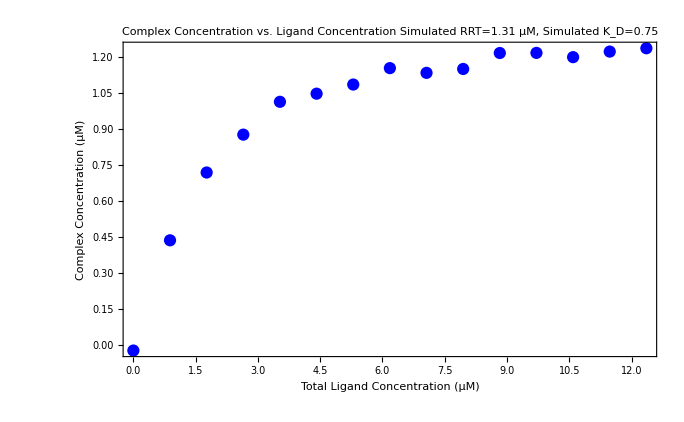

```mathematica
scatterplot = ListPlot[
simdata,
PlotStyle -> Blue,
Frame -> True,
FrameStyle-> Thick,
FrameTicksStyle->{{{Black,18},None},{{Black,18},None}},
FrameLabel ->{Style["Total Ligand Concentration (µM)", Black, 18],Style["Complex Concentration (µM)", Black, 18]},
msg = "Complex Concentration vs. Ligand Concentration\nSimulated RRT=" <> ToString[Round[simRRT, 0.01]] <> " µM, Simulated K_D=" <> ToString[Round[simkd, 0.01]];
PlotLabel -> Style[msg,Black, 18],
ImageSize -> {9 76, 6 72}
]
```

```mathematica
simdata
```

{{0.,-0.0210221},{0.8827,0.437922},{1.7654,0.720054},{2.6481,0.877761},{3.5308,1.01443},{4.4135,1.04823},{5.2962,1.08633},{6.1789,1.15462},{7.0616,1.135},{7.9443,1.15113},{8.827,1.21758},{9.7097,1.21809},{10.5924,1.20033},{11.4751,1.22348},{12.3578,1.23739}}

#### Estimate K_D from the Binding Data

Using NonlinearModelFit.

```mathematica
(* syntax;
NonlinearModelFit[data, model, parameters to fit, independent variable] *)
fit = NonlinearModelFit[simdata, y[x]/. RRT -> simRRT, KD, x]
fit["BestFitParameters"]
```

FittedModel[1/2 (2.1066-√((-2.1066-x)^2-5.22245 x)+x)]

{KD→0.800987}

Create a plot of the fit curve, update the raw data plot with the fit results.

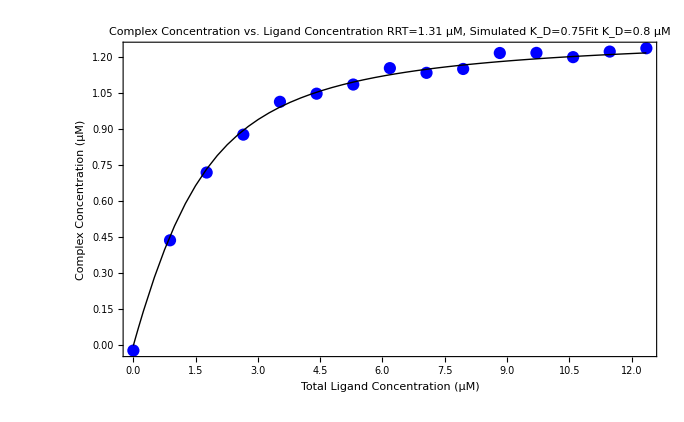

```mathematica
yfit[x_] = Normal[fit ]/. KD -> fit["BestFitParameters"];
msg = "Complex Concentration vs. Ligand Concentration\nRRT=" <> ToString[Round[simRRT, 0.01]] <> " µM, Simulated K_D=" <> ToString[Round[simkd, 0.01]] <> "Fit K_D=" <>  ToString[Round[KD/.fit["BestFitParameters"], 0.01]] <> " µM"; 
fitplot = Plot[yfit[x], {x, 0, simLLTmax}, PlotStyle -> {Black, Thick}, PlotRange -> All];
Show[scatterplot, fitplot, PlotLabel -> Style[msg, Black, 18]]
```